```mathematica
(* solving EOM for quadratic energy loss u *)
 DSolve[{y''[s]+1/(1-u*s^2)*K*y[s]==0, y[0]==y0, y'[0]==0}, y[s],s]
```

{{y[s]→y0 Hypergeometric2F1[-1/4-(√(4 K+u))/(4 √u),-1/4+(√(4 K+u))/(4 √u),1/2,s^2 u]}}

```mathematica
(* solving EOM for linear energy loss u *)
 Simplify[DSolve[{y''[s]+1/(1-u*s)*K*y[s]==0, y[0]==y0, y'[0]==0}, y[s],s]]
```

{{y[s]→-((u^2 √((K (-1+s u))/u^2) y0 ((√(-K/u^2) BesselI[0,2 √(-K/u^2)]+BesselI[1,2 √(-K/u^2)]+√(-K/u^2) BesselI[2,2 √(-K/u^2)]) BesselK[1,2 √((K (-1+s u))/u^2)]+BesselI[1,2 √((K (-1+s u))/u^2)] (√(-K/u^2) BesselK[0,2 √(-K/u^2)]-BesselK[1,2 √(-K/u^2)]+√(-K/u^2) BesselK[2,2 √(-K/u^2)])))/(K ((BesselI[0,2 √(-K/u^2)]+BesselI[2,2 √(-K/u^2)]) BesselK[1,2 √(-K/u^2)]+BesselI[1,2 √(-K/u^2)] (BesselK[0,2 √(-K/u^2)]+BesselK[2,2 √(-K/u^2)]))))}}

```mathematica
(* test for simple case *)
Simplify[DSolve[{y''[s]+(s)*y[s]==0, y[0]==y0, y'[0]==0}, y[s],s]]
```

{{y[s]→1/2 3^(1/6) y0 (√3 AiryAi[(-1)^(1/3) s]+AiryBi[(-1)^(1/3) s]) Gamma[2/3]}}

```mathematica
K = s;
yprimek = Simplify[D[Cos[Sqrt[K]*s]*y0,s]]
ytest = Simplify[Integrate[yprimek, {s,0,s}]]
```

-3/2 √s y0 Sin[s^(3/2)]

y0 (-1+Cos[s^(3/2)])

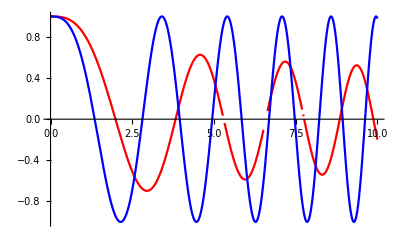

```mathematica
yexact = 1/2 3^(1/6) y0 (√3 AiryAi[(-1)^(1/3) s]+AiryBi[(-1)^(1/3) s]) Gamma[2/3];
Plot[{yexact/.y0->1,ytest+y0/.y0->1}, {s,0,10},PlotStyle->{Red,Blue}]
```

```mathematica
yteqn = Simplify[D[ytest,  {s,2}]+K*ytest]
Limit[ Simplify[D[ytest,  {s,2}]+K*ytest] , s->0]
Simplify[D[yexact,{s,2}]+K*yexact ]
```

1/4 (-4 s y0-5 s y0 Cos[s^(3/2)]-(3 y0 Sin[s^(3/2)])/(√s))

0

0

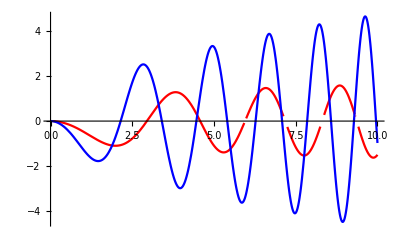

```mathematica
ytp = D[ytest+y0, s]/.y0->1;
yep = D[yexact,s]/.y0->1;
Plot[{yep,ytp}, {s,0,10}, PlotStyle->{Red, Blue}]
```

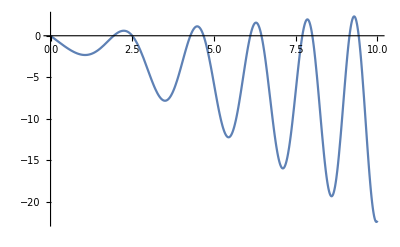

```mathematica
Plot[yteqn/.y0->1, {s,0,10}]
```

```mathematica
Simplify[D[ytp,s]]
Simplify[D[yep,s]]
```

1/4 (-9 s Cos[s^(3/2)]-(3 Sin[s^(3/2)])/(√s))

-1/2 3^(1/6) s (√3 AiryAi[(-1)^(1/3) s]+AiryBi[(-1)^(1/3) s]) Gamma[2/3]

```mathematica
(* checked that eom can be propagated... *)
(** - standard form : no expansion, no energy loss **)
Clear[K]
M00 = {{Cos[Sqrt[K]*(s)], Sin[Sqrt[K]*(s)]/Sqrt[K]},
        {-Sqrt[K]*Sin[Sqrt[K]*(s)], Cos[Sqrt[K]*(s)]}};

M1 = {{Cos[Sqrt[K]*(s2-s1)], Sin[Sqrt[K]*(s2-s1)]/Sqrt[K]},
       {- Sqrt[K]*Sin[Sqrt[K]*(s2-s1)], Cos[Sqrt[K]*(s2-s1)]}};
M0 = {{Cos[Sqrt[K]*(s1)], Sin[Sqrt[K]*(s1)]/Sqrt[K]},
        {-Sqrt[K]*Sin[Sqrt[K]*(s1)], Cos[Sqrt[K]*(s1)]}};
MatrixForm[M1];
MatrixForm[M0];
MatrixForm[Simplify[M1.M0]]
```

(Cos[√K s2] | Sin[√K s2]/(√K)
-√K Sin[√K s2] | Cos[√K s2])

```mathematica
(* diagonalization for limit taking... *)
a={{Cos[Sqrt[K]*(s/N)], Sin[Sqrt[K]*(s/N)]/Sqrt[K]},
        {-Sqrt[K]*Sin[Sqrt[K]*(s/N)], Cos[Sqrt[K]*(s/N)]}};
d=DiagonalMatrix[Eigenvalues[a]];
p=Transpose[Eigenvectors[a]];

(* check reproduce M0 *)
MatrixForm[Simplify[p.d.Inverse[p]]]
```

(Cos[(√K s)/N] | Sin[(√K s)/N]/(√K)
-√K Sin[(√K s)/N] | Cos[(√K s)/N])

```mathematica
m0inf = Simplify[ Limit[p.MatrixPower[d,N].Inverse[p], N->∞] ];
MatrixForm[m0inf]
(* m0inf == M00 : TRUE! *)
```

(1/2 ⅇ^(-ⅈ √K s) (1+ⅇ^(2 ⅈ √K s)) | -(ⅈ ⅇ^(-ⅈ √K s) (-1+ⅇ^(2 ⅈ √K s)))/(2 √K)
1/2 ⅈ ⅇ^(-ⅈ √K s) (-1+ⅇ^(2 ⅈ √K s)) √K | 1/2 ⅇ^(-ⅈ √K s) (1+ⅇ^(2 ⅈ √K s)))

```mathematica
(** - w/ expansion (to 2nd order), no energy loss **)
```

```mathematica
(* diagonalization for limit taking... *)
Clear[a,d,p,m0inf]
a={{1-(Sqrt[K]*s/N)^2, (s/N)},
   {-K*s/N, 1-(Sqrt[K]*s/N)^2}};
d=DiagonalMatrix[Eigenvalues[a]];
p=Transpose[Eigenvectors[a]];
MatrixForm[a]
```

(1-(K s^2)/N^2 | s/N
-(K s)/N | 1-(K s^2)/N^2)

```mathematica
m0inf = Simplify[ Limit[p.MatrixPower[d,N].Inverse[p], N->∞] ];
MatrixForm[m0inf]
(* equals the cos / sin form *)
```

(1/2 ⅇ^(-ⅈ √K s) (1+ⅇ^(2 ⅈ √K s)) | -(ⅈ ⅇ^(-ⅈ √K s) (-1+ⅇ^(2 ⅈ √K s)))/(2 √K)
1/2 ⅈ ⅇ^(-ⅈ √K s) (-1+ⅇ^(2 ⅈ √K s)) √K | 1/2 ⅇ^(-ⅈ √K s) (1+ⅇ^(2 ⅈ √K s)))

```mathematica
(** - w/ expansion (to 2nd order), linear energy loss **)
```

```mathematica
(*** -- expansion... ***)
Series[Cos[Sqrt[K*(1/(1-u*s/N))]*s/N],{s,0,5}];
Series[-Sqrt[K*(1/(1-u*s))]*Sin[Sqrt[K*(1/(1-u*s))]*s/N],{s,0,5}];
Series[Sin[Sqrt[K*(1/(1-u*s/N))]*s/N]/Sqrt[K*(1/(1-u*s/N))],{s,0,5}];
```

```mathematica
(*** -- diagonalization... ***)
Clear[a,d,p,m0inf,m1inf]
a={{1-(K s^2)/(2 N^2), (s/N)},
   {-(K s)/N-(K u s^2)/N^2, 1-(K s^2)/(2 N^2)}};
d=DiagonalMatrix[Eigenvalues[a]];
p=Transpose[Eigenvectors[a]];
MatrixForm[a]
```

(1-(K s^2)/(2 N^2) | s/N
-(K s)/N-(K s^2 u)/N^2 | 1-(K s^2)/(2 N^2))

```mathematica
(** - this won't work since each p[s] is different **)
m0inf = Simplify[ Limit[p.MatrixPower[d,N].Inverse[p], N->∞] ];
MatrixForm[m0inf]
```

(1/2 ⅇ^(-√(-K s^2)) (1+ⅇ^(2 √(-K s^2))) | (ⅇ^(-√(-K s^2)) (-1+ⅇ^(2 √(-K s^2))) s)/(2 √(-K s^2))
(ⅇ^(-√(-K s^2)) (-1+ⅇ^(2 √(-K s^2))) √(-K s^2))/(2 s) | 1/2 ⅇ^(-√(-K s^2)) (1+ⅇ^(2 √(-K s^2))))

```mathematica
(** instead, try direct limit **)
(*  - though it turned out that the answers are the same... -*)
m1inf = Simplify[ Limit[MatrixPower[a,N], N->∞] ];
MatrixForm[m1inf]
(*  - couldn't work since 'u' was normalized to N^2... - *)
```

(1/2 ⅇ^(-√(-K s^2)) (1+ⅇ^(2 √(-K s^2))) | (ⅇ^(-√(-K s^2)) (-1+ⅇ^(2 √(-K s^2))) s)/(2 √(-K s^2))
-(ⅇ^(-√(-K s^2)) (-1+ⅇ^(2 √(-K s^2))) K s)/(2 √(-K s^2)) | 1/2 ⅇ^(-√(-K s^2)) (1+ⅇ^(2 √(-K s^2))))

```mathematica
(* solving EOM for quadratic energy loss u *)
 Simplify[DSolve[{y''[s]+1/(1-v*s^2)*K*y[s]==0, y[0]==y0, y'[0]==0}, y[s],s]]
```

{{y[s]→y0 Hypergeometric2F1[-1/4-(√(4 K+v))/(4 √v),1/4 (-1+(√(4 K+v))/(√v)),1/2,s^2 v]}}

```mathematica
(** - w/ expansion (to 2nd order), linear energy loss **)
```

```mathematica
(*** -- expansion... ***)
Series[Cos[Sqrt[K*(1/(1-v*s^2/N))]*s/N],{s,0,5}];
Series[-Sqrt[K*(1/(1-v^2*s))]*Sin[Sqrt[K*(1/(1-v*s^2))]*s/N],{s,0,5}];
Series[Sin[Sqrt[K*(1/(1-v*s^2/N))]*s/N]/Sqrt[K*(1/(1-v*s^2/N))],{s,0,5}];
```

```mathematica
Clear[a,d,p,m0inf,m1inf]
(*** --- 3rd order, otherwise no correction --- ***)
a={{1-(K s^2)/(2 N^2), s/N-(K s^3)/(6 N^3)},
   {-(K s)/N+((K^2-6 K v) s^3)/(6 N^3), 1-(K s^2)/(2 N^2)}};
d=DiagonalMatrix[Eigenvalues[a]];
p=Transpose[Eigenvectors[a]];
MatrixForm[a]
```

(1-(K s^2)/(2 N^2) | s/N-(K s^3)/(6 N^3)
-(K s)/N+(s^3 (K^2-6 K v))/(6 N^3) | 1-(K s^2)/(2 N^2))

```mathematica
m1inf = Simplify[ Limit[MatrixPower[a,N], N->∞] ];
MatrixForm[m1inf]
```

(1/2 ⅇ^(-√(-K s^2)) (1+ⅇ^(2 √(-K s^2))) | (ⅇ^(-√(-K s^2)) (-1+ⅇ^(2 √(-K s^2))) s)/(2 √(-K s^2))
(ⅇ^(-√(-K s^2)) (-1+ⅇ^(2 √(-K s^2))) √(-K s^2))/(2 s) | 1/2 ⅇ^(-√(-K s^2)) (1+ⅇ^(2 √(-K s^2))))

```mathematica
y1v = y0 Hypergeometric2F1[-1/4-(√(4 K+v))/(4 √v),1/4 (-1+(√(4 K+v))/(√v)),1/2,s^2 v];
(* --- same as above linear case ... ---*)
(*Plot[{y1v/.{y0->1, v->0.001, K->0.01},Cos[Sqrt[K]*s]/.{K->0.01},Cosh[Sqrt[-K s^2 (2+s v^2)/2]]/.{v->0.001, K->0.01}}, {s,0,16},PlotStyle->{Red,Blue,Green}]*)
```

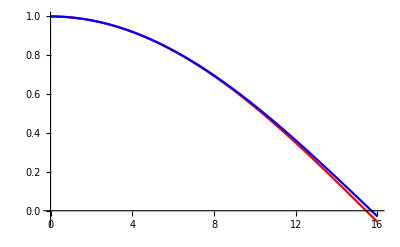

```mathematica
Plot[{y1v/.{y0->1, v->0.001, K->0.01},Cos[Sqrt[K]*s]/.{K->0.01}}, {s,0,16},PlotStyle->{Red,Blue}]
```

```mathematica
(**  How about direct substitution? **)
Clear[a,d,p,b,dd,pp,m0inf,m1inf]
(*** --- linear --- ***)
a={{Cos[Sqrt[K*(1/(1-u*s/N))]*s/N], -Sqrt[K*(1/(1-u*s/N))]*Sin[Sqrt[K*(1/(1-u*s/N))]*s/N]},
   {Sin[Sqrt[K*(1/(1-u*s/N))]*s/N]/Sqrt[K*(1/(1-u*s/N))], Cos[Sqrt[K*(1/(1-u*s/N))]*s/N]}};
dd=DiagonalMatrix[Eigenvalues[a]];
pp=Transpose[Eigenvectors[a]];
MatrixForm[a]

(*** --- quadratic --- ***)
b={{Cos[Sqrt[K*(1/(1-v*(s/N)^2))]*s/N], -Sqrt[K*(1/(1-v*(s/N)^2))]*Sin[Sqrt[K*(1/(1-v*(s/N)^2))]*s/N]},
   {Sin[Sqrt[K*(1/(1-v*(s/N)^2))]*s/N]/Sqrt[K*(1/(1-v*(s/N)^2))], Cos[Sqrt[K*(1/(1-v*(s/N)^2))]*s/N]}};
dd=DiagonalMatrix[Eigenvalues[a]];
pp=Transpose[Eigenvectors[a]];
MatrixForm[b]
```

(Cos[(s √(K/(1-(s u)/N)))/N] | -√(K/(1-(s u)/N)) Sin[(s √(K/(1-(s u)/N)))/N]
Sin[(s √(K/(1-(s u)/N)))/N]/(√(K/(1-(s u)/N))) | Cos[(s √(K/(1-(s u)/N)))/N])

(Cos[(s √(K/(1-(s^2 v)/N^2)))/N] | -√(K/(1-(s^2 v)/N^2)) Sin[(s √(K/(1-(s^2 v)/N^2)))/N]
Sin[(s √(K/(1-(s^2 v)/N^2)))/N]/(√(K/(1-(s^2 v)/N^2))) | Cos[(s √(K/(1-(s^2 v)/N^2)))/N])

```mathematica
y00 = y0*Cos[Sqrt[K]*s1];
Pp = -K*v*s1^2*y00;

Cc = Cos[Sqrt[K]*s];
Ss =Sin[Sqrt[K]*s]/Sqrt[K];
Gg = (Ss*(Cc/.s->s1)-Cc*(Ss/.s->s1))
```

(Cos[√K s1] Sin[√K s])/(√K)-(Cos[√K s] Sin[√K s1])/(√K)

```mathematica
Gint = Integrate[Gg*Pp, {s1,0,s}]
```

-(s v y0 (3 √K s Cos[√K s]+(-3+2 K s^2) Sin[√K s]))/(12 √K)

```mathematica
Solve[{{(Aa*Cc+Bb*Ss+Dd*Gint)/.s->0}==y0, {D[(Aa*Cc+Bb*Ss+Dd*Gint),s]/.s->0}==0}, {Aa,Bb}]
```

{{Aa→y0,Bb→0}}

```mathematica
Simplify[D[Gint,{s,2}]+K*(1)*Gint]
```

-K s^2 v y0 Cos[√K s]

```mathematica
ygreen = y0*Cc+Gint;
ydiff = Simplify[D[ygreen,{s,2}]+K*(1+v*s^2)*ygreen]
```

-1/12 √K s^3 v^2 y0 (3 √K s Cos[√K s]+(-3+2 K s^2) Sin[√K s])

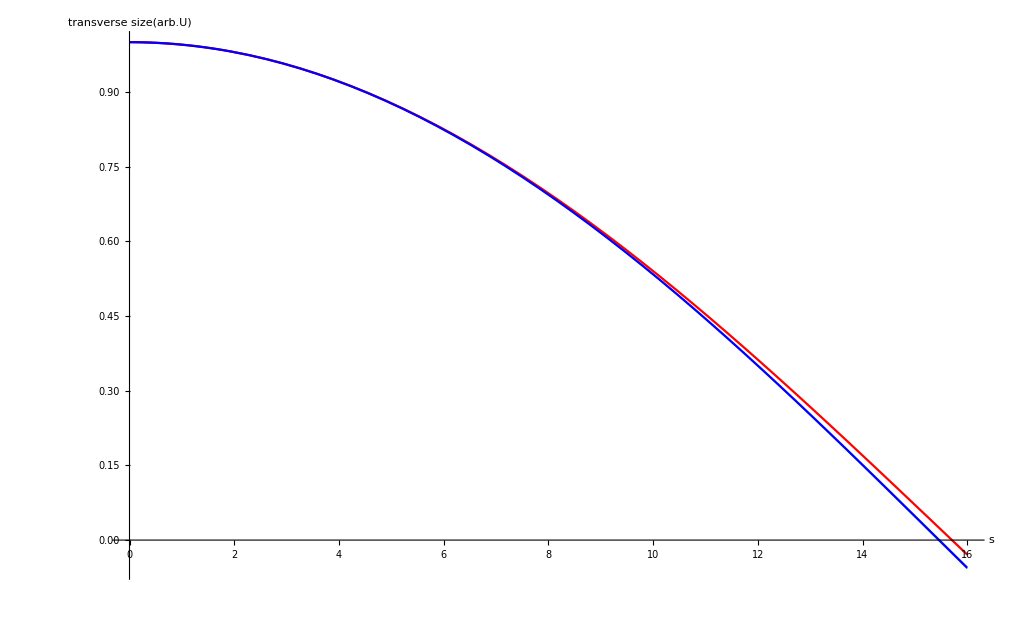

```mathematica
Plot[{y1v/.{y0->1, v->0.001, K->0.01},Cos[Sqrt[K]*s]/.{K->0.01},ygreen/.{y0->1, v->0.001, K->0.01}}, {s,0,16},PlotStyle->{Thick,Red,Blue,Green},AxesLabel->{HoldForm[s],HoldForm[transverse size[arb.U]]},PlotLabel->None,LabelStyle->{18,GrayLevel[0],Bold}]
(* Very beautiful ! Green almost matches Red!!! *)
```

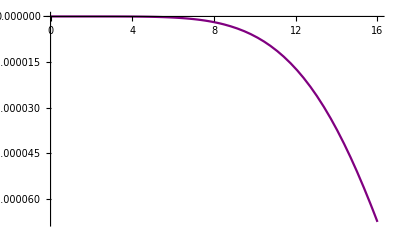

```mathematica
Plot[ydiff/.{y0->1, v->0.001, K->0.01}, {s,0,16},PlotStyle->{Purple}]
```

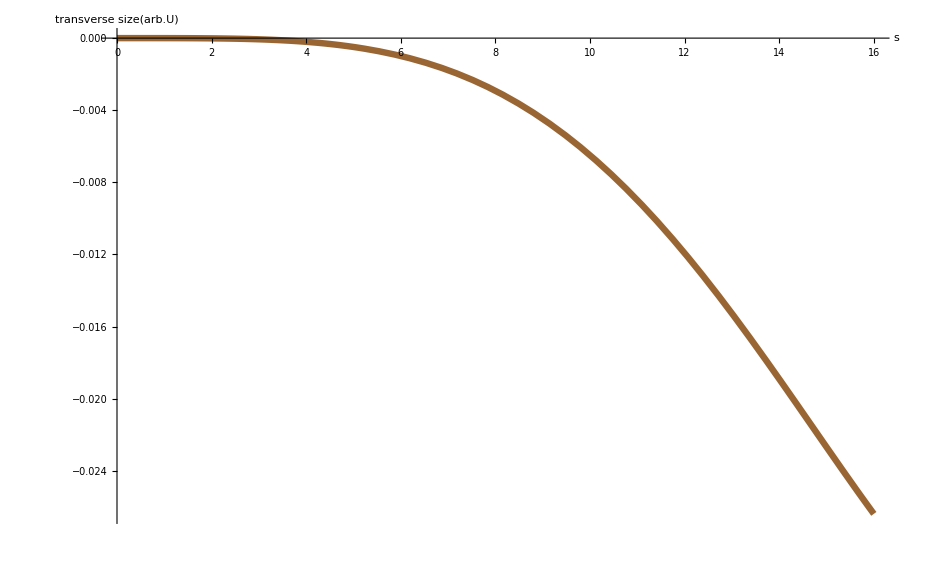

```mathematica
(* residual == Gint *)
Plot[Gint/.{y0->1, v->0.001, K->0.01}, {s,0,16},PlotStyle->{Thickness[0.005],Brown},AxesLabel->{HoldForm[s],HoldForm[transverse size[arb.U]]},PlotLabel->None,LabelStyle->{18,GrayLevel[0],Bold}]
```

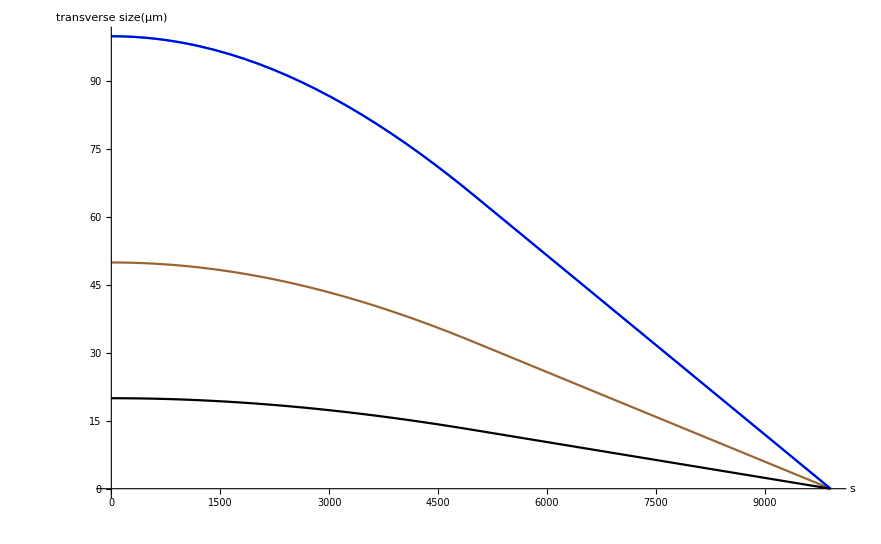

```mathematica
(** Free space drift **)
Ccc = y0*Cc*UnitStep[L-s];
y10 = y0*D[Cc,s]/.s->L;
Ccl = (y0*Cc/.s->L)*UnitStep[s-L];
Ccf = Ccc+(Ccl+UnitStep[s-L]*y10*(s-L));

Gcc = ygreen*UnitStep[L-s];
g10 = D[ygreen,s]/.s->L;
Ggl = (ygreen/.s->L)*UnitStep[s-L];
Ggf = Gcc+Ggl+UnitStep[s-L]*g10*(s-L);

vcc = y1v*UnitStep[L-s];
v10 = D[y1v,s]/.s->L;
vvl = (y1v/.s->L)*UnitStep[s-L];
vvf = vcc+vvl+UnitStep[s-L]*v10*(s-L);

Plot[{{Ggf/.{v->7*10^-4/L^2}}/.{L->5000,K->3*10^-8,y0->100},{Ggf/.{v->7*10^-4/L^2}}/.{L->5000,K->3*10^-8,y0->50} ,{Ggf/.{v->7*10^-4/L^2}}/.{L->5000,K->3*10^-8,y0->20} ,Ccf/.{L->5000,K->3*10^-8,y0->100}},{s,0,9920},PlotStyle->{Green,Brown,Black,Blue},PlotRange->{0,100},AxesLabel->{HoldForm[s],HoldForm[transverse size [μm]]},PlotLabel->None,LabelStyle->{18,GrayLevel[0],Bold}]
```

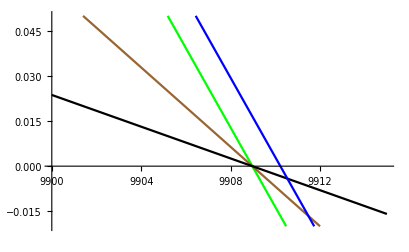

```mathematica
Plot[{{Ggf/.{v->7*10^-4/L^2}}/.{L->5000,K->3*10^-8,y0->100},{Ggf/.{v->7*10^-4/L^2}}/.{L->5000,K->3*10^-8,y0->50} ,{Ggf/.{v->7*10^-4/L^2}}/.{L->5000,K->3*10^-8,y0->20} ,Ccf/.{L->5000,K->3*10^-8,y0->100}},{s,9900,9915},PlotStyle->{Green,Brown,Black,Blue},PlotRange->{-0.02,0.05}]
```

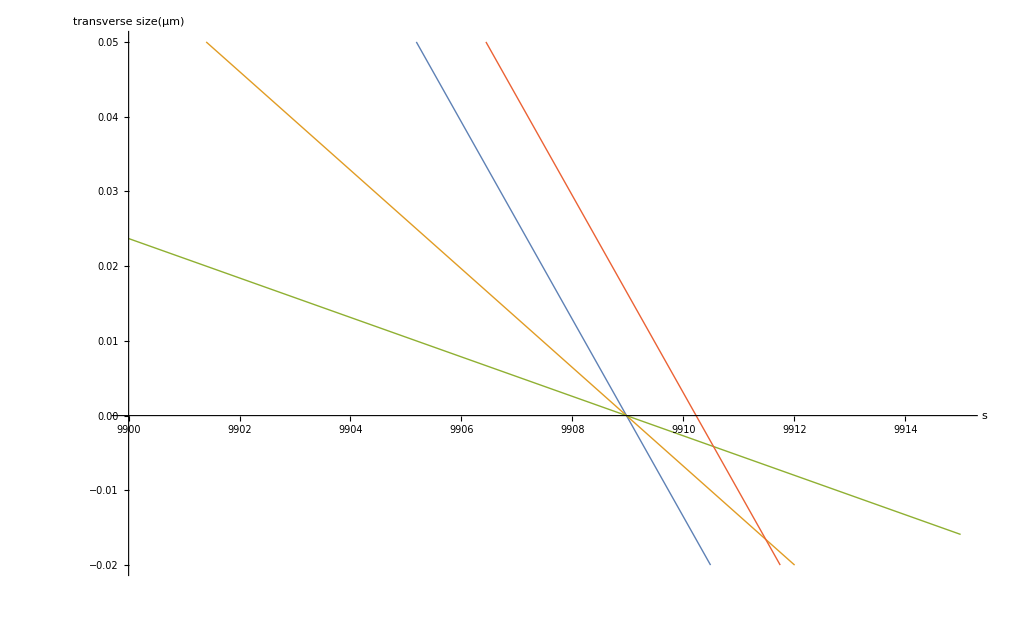

```mathematica
Plot[{{vvf/.{v->7*10^-4/L^2}}/.{L->5000,K->3*10^-8,y0->100},{vvf/.{v->7*10^-4/L^2}}/.{L->5000,K->3*10^-8,y0->50} ,{vvf/.{v->7*10^-4/L^2}}/.{L->5000,K->3*10^-8,y0->20} ,Ccf/.{L->5000,K->3*10^-8,y0->100}},{s,9900,9915},PlotStyle->{Thick},PlotRange->{-0.02,0.05},AxesLabel->{HoldForm[s],HoldForm[transverse size [μm]]},PlotLabel->None,LabelStyle->{18,GrayLevel[0],Bold}]
```

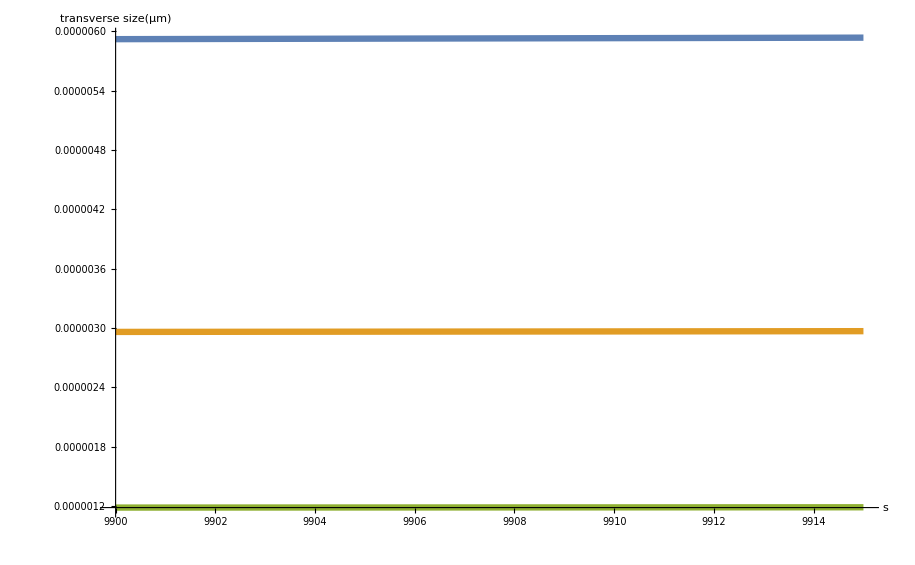

```mathematica
(**** difference between exact and ygreen ****)
Plot[{{(-vvf+Ggf)/.{v->7*10^-4/L^2}}/.{L->5000,K->3*10^-8,y0->100},{(-vvf+Ggf)/.{v->7*10^-4/L^2}}/.{L->5000,K->3*10^-8,y0->50} ,{(-vvf+Ggf)/.{v->7*10^-4/L^2}}/.{L->5000,K->3*10^-8,y0->20}} ,{s,9900,9915},PlotStyle->{Thickness[0.005]},AxesLabel->{HoldForm[s],HoldForm[transverse size [μm]]},PlotLabel->None,LabelStyle->{18,GrayLevel[0],Bold}]
```

```mathematica
(* where is zero *)
(** - unperturbed - **)
Solve[-√K (-L+s) y0 Sin[√K L]+y0 Cos[√K L]==0,s]
```

{{s→(√K L+Cot[√K L])/(√K)}}

```mathematica
(*** i.e., l* = s-L = ***)
last=Simplify[(√K L+Cot[√K L])/(√K)-L]
```

Cot[√K L]/(√K)

```mathematica
(*** i.e., s=9910.23 ***)
N[last/.{K->3*10^-8,L->5000}]
```

4910.23

```mathematica
(** - ygreen, outside lens - **)
Ggout = Simplify[(-L+s) (-√K y0 Sin[√K L]-(L v y0 (3 √K Cos[√K L]+√K (-3+2 K L^2) Cos[√K L]+K L Sin[√K L]))/(12 √K)-(v y0 (3 √K L Cos[√K L]+(-3+2 K L^2) Sin[√K L]))/(12 √K))+(y0 Cos[√K L]-(L v y0 (3 √K L Cos[√K L]+(-3+2 K L^2) Sin[√K L]))/(12 √K))]
```

(y0 (√K (12+2 K L^3 (L-s) v-3 L s v) Cos[√K L]+(3 s v+K (12 L-12 s+L^3 v-3 L^2 s v)) Sin[√K L]))/(12 √K)

```mathematica
(*** different y0 different deviations ***)
N[{Ggout/.{v->7*10^-4/L^2}}/.{K->3*10^-8,L->5000,y0->100,s->9910.23}]
N[{Ggout/.{v->7*10^-4/L^2}}/.{K->3*10^-8,L->5000,y0->50,s->9910.23}]
N[{Ggout/.{v->7*10^-4/L^2}}/.{K->3*10^-8,L->5000,y0->20,s->9910.23}]
```

{-0.0165462}

{-0.0082731}

{-0.00330924}

```mathematica
(** - y1v, outside lens - **)
```

```mathematica
vvout=Simplify[y0 Hypergeometric2F1[-1/4-(√(4 K+v))/(4 √v),1/4 (-1+(√(4 K+v))/(√v)),1/2,L^2 v]+L (-L+s) v (-1/4-(√(4 K+v))/(4 √v)) (-1+(√(4 K+v))/(√v)) y0 Hypergeometric2F1[3/4-(√(4 K+v))/(4 √v),1+1/4 (-1+(√(4 K+v))/(√v)),3/2,L^2 v]]
```

y0 (Hypergeometric2F1[-1/4-(√(4 K+v))/(4 √v),1/4 (-1+(√(4 K+v))/(√v)),1/2,L^2 v]+K L (L-s) Hypergeometric2F1[3/4-(√(4 K+v))/(4 √v),1/4 (3+(√(4 K+v))/(√v)),3/2,L^2 v])

```mathematica
(*** different y0 different deviations ***)
```

```mathematica
N[{vvout/.{v->7*10^-4/L^2}}/.{K->3*10^-8,L->5000,y0->100,s->9910.23}]
N[{vvout/.{v->7*10^-4/L^2}}/.{K->3*10^-8,L->5000,y0->50,s->9910.23}]
N[{vvout/.{v->7*10^-4/L^2}}/.{K->3*10^-8,L->5000,y0->20,s->9910.23}]
```

{-0.0165521}

{-0.00827607}

{-0.00331043}

```mathematica
(* where is zero - full solution*)
(** - unperturbed - **)
ini = {{yo},{y1o}};

unpfd = {{1,l},{0,1}};
unpln = {{Cc, Ss},{-K*Ss, Cc}}/.s->L;

unpyl = Simplify[unpfd.unpln.ini]
```

{{(√K (l y1o+yo) Cos[√K L]+(y1o-K l yo) Sin[√K L])/(√K)},{y1o Cos[√K L]-√K yo Sin[√K L]}}

```mathematica
(*** check consistency ***)
Solve[{unpyl[[1,1]]/.y1o->0}==0,l]
```

{{l→Cot[√K L]/(√K)}}

```mathematica
(** - ygreen - **)
ygfd = unpfd/.l->4910.23;
```

```mathematica
Clear[Aa,Bb,y0,y11,y00,y01];
y00 = y0*Cos[Sqrt[K]*s1];
y01 = y11*Sin[Sqrt[K]*s1]/Sqrt[K];
Pp = -K*v*s1^2*(y00+y01);

Gint = Integrate[Gg*Pp, {s1,0,s}]
```

-(v (-√K s (-3 y11+K s (-3 y0+2 s y11)) Cos[√K s]+(2 K^2 s^3 y0-3 y11+3 K s (-y0+s y11)) Sin[√K s]))/(12 K^(3/2))

```mathematica
Solve[{{(Aa*Cc+Bb*Ss+Gint)/.s->0}==y0, {D[(Aa*Cc+Bb*Ss+Gint),s]/.s->0}==y11}, {Aa,Bb}]
```

{{Aa→y0,Bb→y11}}

```mathematica
Aa = y0;
Bb =y11;
```

```mathematica
ygful = Aa*Cc+Bb*Ss+Gint;
ygfpr = D[ygful,s];

ygstar ={ ygful/.s->L}+{{ygfpr/.s->L}*l};
```

```mathematica
(**** note y10 is radians; ϵ=1/γ~10^-4 (μm) + σ0~1 => β~10^8, so y'~10^-6 ****)
N[{ygstar/.{v->7*10^-4/L^2}}/.{K->3*10^-8,L->5000,y0->100,y10->10^-6,l->4910.23}]
```

{{{-0.00896704}}}

```mathematica
Simplify[ygstar]
```

{{1/(12 √K)(-√K ((-12+3 l L v+3 L^2 v+2 K l L^3 v) y0-12 l y10) Cos[√K L]+(-K (2 L^3 v+3 l (4+L^2 v)) y0+3 (l v y0+L v y0+4 y10)) Sin[√K L])}}

```mathematica
(** - y1v - **)
Clear[y0,y10,s];
Simplify[DSolve[{x''[s]+1/(1-v*s^2)*K*x[s]==0, x[0]==y0, x'[0]==y10}, x[s],s]]
```

{{x[s]→y0 Hypergeometric2F1[-1/4-(√(4 K+v))/(4 √v),1/4 (-1+(√(4 K+v))/(√v)),1/2,s^2 v]+s y10 Hypergeometric2F1[1/4-(√(4 K+v))/(4 √v),1/4 (1+(√(4 K+v))/(√v)),3/2,s^2 v]}}

```mathematica
y2ful = y0 Hypergeometric2F1[-1/4-(√(4 K+v))/(4 √v),1/4 (-1+(√(4 K+v))/(√v)),1/2,s^2 v]+s y11 Hypergeometric2F1[1/4-(√(4 K+v))/(4 √v),1/4 (1+(√(4 K+v))/(√v)),3/2,s^2 v];
y2vpr = D[y2ful,s];
y2star = { y2ful/.s->L}+{{y2vpr/.s->L}*l};
```

```mathematica
Simplify[y2vpr]
```

y11 Hypergeometric2F1[1/4-(√(4 K+v))/(4 √v),1/4 (1+(√(4 K+v))/(√v)),3/2,s^2 v]-1/3 K s (3 y0 Hypergeometric2F1[3/4-(√(4 K+v))/(4 √v),1/4 (3+(√(4 K+v))/(√v)),3/2,s^2 v]+s y11 Hypergeometric2F1[5/4-(√(4 K+v))/(4 √v),1/4 (5+(√(4 K+v))/(√v)),5/2,s^2 v])

```mathematica
N[{y2star/.{v->7*10^-4/L^2}}/.{K->3*10^-8,L->5000,y0->100,y10->10^-6,l->4910.23}]
```

{{{-0.00897367}}}

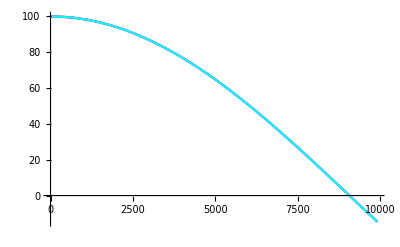

```mathematica
(**** note, this has NO free-drift ****)
Plot[{{y2ful/.{v->7*10^-4/L^2}}/.{K->3*10^-8,L->5000,y0->100,y10->10^-5},{y2ful/.{v->7*10^-4/L^2}}/.{K->3*10^-8,L->5000,y0->100,y10->10^-6},{y2ful/.{v->7*10^-4/L^2}}/.{K->3*10^-8,L->5000,y0->100,y10->10^-7}},{s,0,9920},PlotStyle->{Orange,Magenta,Cyan}]
```

```mathematica
(**** including FS drift ****)
v2cc = y2ful*UnitStep[L-s];
v210 = D[y2ful,s]/.s->L;
v2vl = (y2ful/.s->L)*UnitStep[s-L];
v2vf = v2cc+v2vl+UnitStep[s-L]*v210*(s-L);

Clear[y0,y11];
C2c = (y0*Cc+y11*Ss)*UnitStep[L-s];
y20 = D[(y0*Cc+y11*Ss),s]/.s->L;
C2l = ((y0*Cc+y11*Ss)/.s->L)*UnitStep[s-L];
C2f = Ccc+(Ccl+UnitStep[s-L]*y20*(s-L));
```

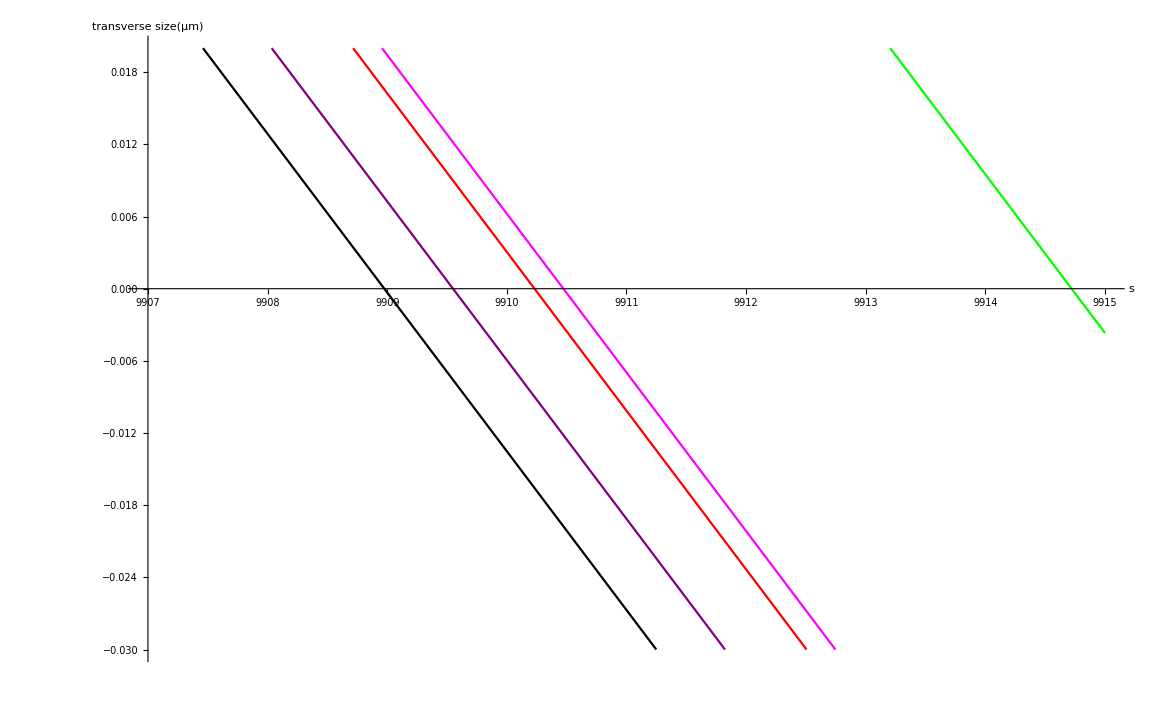

```mathematica
(**** - much smaller effect than σ0 - ****)
Plot[{{v2vf/.{v->7*10^-4/L^2}}/.{L->5000,K->3*10^-8,y0->100,y11->10^-5},{v2vf/.{v->7*10^-4/L^2}}/.{L->5000,K->3*10^-8,y0->100,y11->10^-6} ,{v2vf/.{v->7*10^-4/L^2}}/.{L->5000,K->3*10^-8,y0->100,y11->0} ,C2f/.{L->5000,K->3*10^-8,y0->100,y11->10^-6},C2f/.{L->5000,K->3*10^-8,y0->100,y11->0}},{s,9907,9915},PlotStyle->{Green,Purple,Black,Magenta,Red},PlotRange->{-0.03,0.02},AxesLabel->{HoldForm[s],HoldForm[transverse size [μm]]},PlotLabel->None,LabelStyle->{18,GrayLevel[0],Bold}]
```

```mathematica
(* Wakefield energy loss distribution *)
(**- wakefield -**)
Clear[a,z];
p1 = 1/Sqrt[4π]*2^(4/3)*Gamma[5/6]*Hypergeometric1F1[2/3,1/2,-(z/a)^2/2];
p2 = -1/Sqrt[4π]*2^(5/6)*Gamma[3/4]*(z/a)*Hypergeometric1F1[7/6,3/2,-(z/a)^2/2];
pt=p1+p2;

(**- Gaussian bunch -**)
gaus = 1/Sqrt[2π]/a*Exp[-z^2/2/a^2];

(**- normalization : to P_tot -**)
(*** NOTE: the integration is for d(z/a); here I rewrite it by a->1 ***)
(**** normp * 0.55 (=(√(2/π))/3^(1/3)) -> 0.35 =(3^(1/6) Gamma[2/3]^2)/(2 π) ****)
normp = 0.35/0.55/Integrate[pt*gaus/.a->1, {z,-∞,∞}, GenerateConditions->False];
```

Plot[%1138,AxesLabel→{s,transverse size[μm]},PlotLabel→None,LabelStyle→{18,GrayLevel[0],Bold}]

```mathematica
normp
```

1.25896

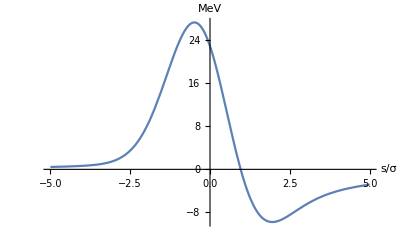

```mathematica
(**- energy loss due to wakefield -**)
(**** unit : MeV, length in cm ****)
ee = 4.8*10^-10;
ff = 0.55*ee^2*624151; (* 1erg = 624151 MeV *)
dEdtwake =ff*N/(ρ^(2/3))/(σ^(4/3))*normp*pt;
Plot[dEdtwake/.{N->1.4*10^10,ρ->34.1,a->1,σ->10^-4},{z,-5,5},AxesLabel->{HoldForm[s/σ],HoldForm[MeV]}]
```

```mathematica
(**** NOTE: this differs from the Sheet by a factor of 2 due to diff conventions ****)
Integrate[dEdtwake*gaus/.{N->1.4*10^10,ρ->34.1,a->1,σ->10^-4},{z,-∞,∞}]*0.5
```

7.21831

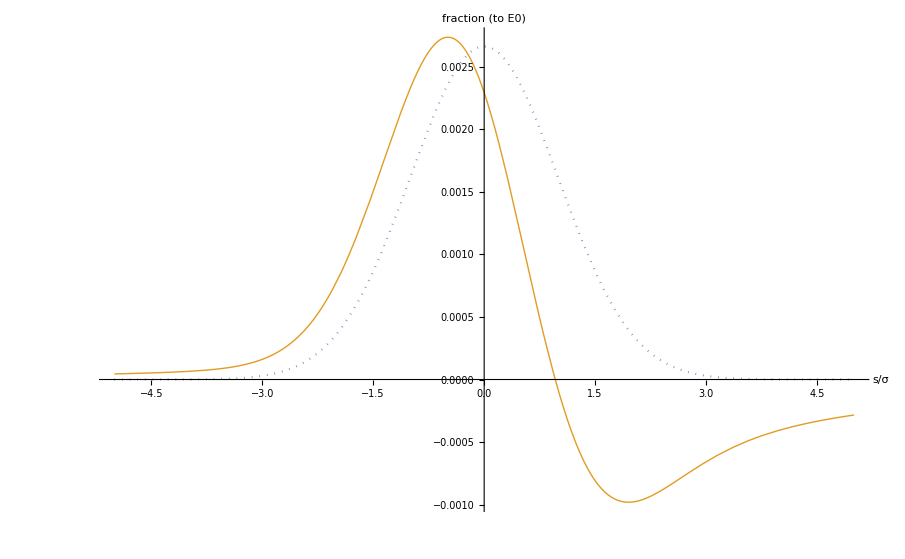

```mathematica
fracwake = 0.001/10*dEdtwake;
vwake = fracwake/L^2;
Plot[Evaluate@Table[{gaus/150,fracwake}/.{N->1.4*10^10,ρ->34.1,a->1,σ->10^-4}],{z,-5,5},AxesLabel->{HoldForm[s/σ],HoldForm[fraction (to E0)]},PlotStyle->{Dotted,Thick},LabelStyle->{18,GrayLevel[0],Bold}]
```

```mathematica
(**** note here we must use L=5000 μm, but other parameters still in cm ****)
(*** -- total power loss (P/2 = v(L^2/2) -- ***)
Integrate[vwake*gaus/.{L->5000,N->1.4*10^10,ρ->34.1,a->1,σ->10^-4},{z,-∞,∞}]*5000^2
```

0.00144366

```mathematica
(** slices ; start from -5σ to +5σ **)
NN = 99;
step = 10/NN;
ss[i_] = -5+step*i;

(**** starts from i=0 to i=NN ****)
wakesli[i_] = vwake/.z->ss[i];
```

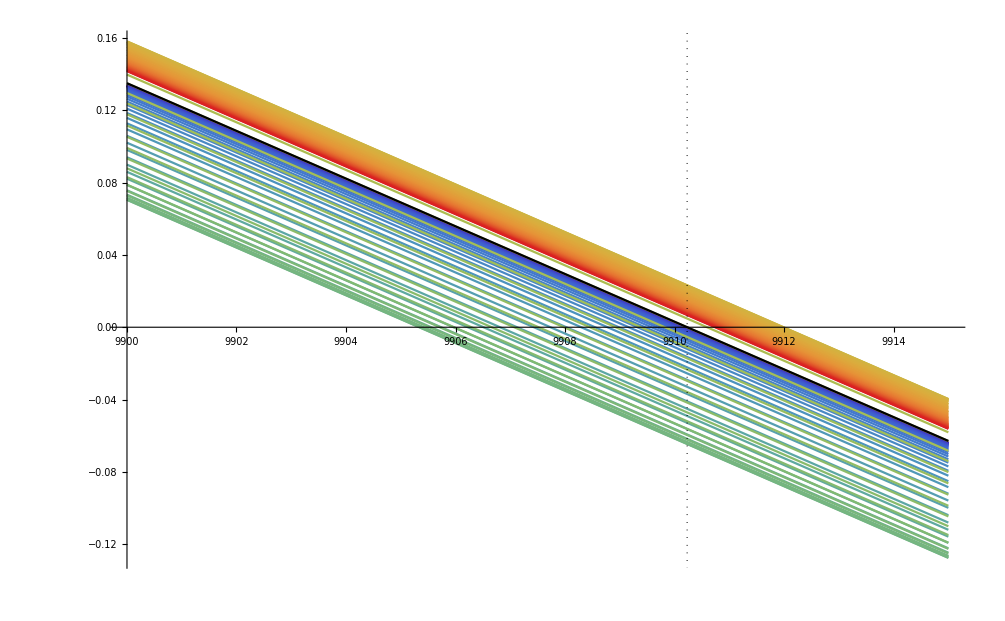

```mathematica
(*** since the exact soln is not continuous, we have to use ygreen ***)
wakelist = Table[Ggf/.v->wakesli[j],{j,0,NN}];
clr = Table[ColorData["Rainbow",i/NN],{i,0,NN}]~Join~{Black};
Plot[{Evaluate[wakelist/.{L->5000,K->3*10^-8,y0->100,N->1.4*10^10,ρ->34.1,a->1,σ->10^-4}],Ccf/.{L->5000,K->3*10^-8,y0->100}},{s,9900,9915},PlotStyle->clr,Epilog->{Dotted, Thick, Line[{{9910.23,-1},{9910.23,1}}]},LabelStyle->{18,GrayLevel[0],Bold}]
```

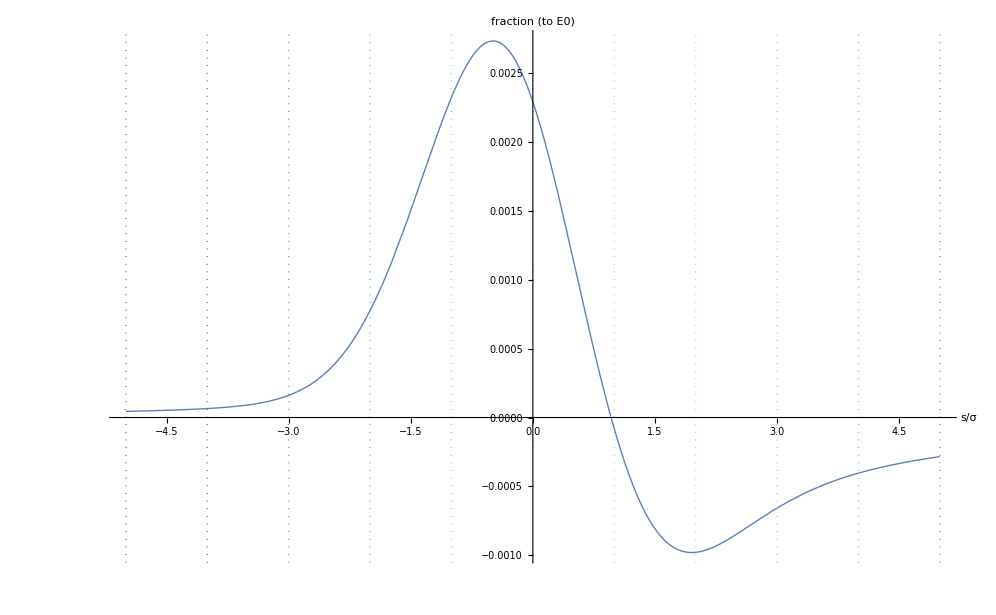

```mathematica
linlist = Table[{Thick,Dotted,clr[[i]],Line[{{ss[i-1],-1},{ss[i-1],1}}]},{i,1,NN+1}];
Plot[{fracwake/.{N->1.4*10^10,ρ->34.1,a->1,σ->10^-4}},{z,-5,5},AxesLabel->{HoldForm[s/σ],HoldForm[fraction (to E0)]},Epilog->linlist,PlotStyle->Thick,LabelStyle->{18,GrayLevel[0],Bold}]
```

```mathematica
sizel = N[wakelist/.{L->5000,K->3*10^-8,y0->100,N->1.4*10^10,ρ->34.1,a->1,σ->10^-4,s->9910.23}]
```

{-0.0010377,-0.00107099,-0.0011065,-0.00114453,-0.00118547,-0.00122982,-0.00127824,-0.00133157,-0.00139094,-0.00145779,-0.00153406,-0.00162225,-0.00172559,-0.00184827,-0.00199561,-0.00217429,-0.00239268,-0.00266101,-0.00299167,-0.00339942,-0.00390152,-0.00451778,-0.00527043,-0.00618384,-0.00728399,-0.00859764,-0.0101512,-0.0119696,-0.0140739,-0.0164802,-0.0191969,-0.0222227,-0.0255446,-0.0291356,-0.0329537,-0.0369408,-0.0410229,-0.0451104,-0.0491004,-0.0528799,-0.056329,-0.0593262,-0.0617538,-0.0635034,-0.0644821,-0.0646172,-0.0638615,-0.0621961,-0.059633,-0.0562149,-0.0520146,-0.0471317,-0.0416881,-0.0358229,-0.0296856,-0.0234298,-0.0172057,-0.0111546,-0.00540303,-0.0000584399,0.00479379,0.009092,0.0127986,0.0158989,0.0183992,0.0203242,0.021713,0.0226159,0.0230905,0.0231983,0.0230014,0.0225603,0.0219313,0.0211657,0.020308,0.0193963,0.0184618,0.0175293,0.0166175,0.0157402,0.0149066,0.0141221,0.0133894,0.012709,0.0120795,0.0114987,0.0109636,0.0104708,0.0100166,0.00959771,0.00921067,0.00885236,0.00851992,0.00821076,0.00792254,0.00765322,0.00740097,0.00716416,0.00694139,0.00673141}

```mathematica
(**** weighted spot size (by Gaussian bunch dist. in between +/- 1/2 step_ !!! ****)
(** -- density : so divided by step -- **)
(*** check sum up to 1 ***)
dens = Table[N[Integrate[gaus,{z,ss[i]-0.5*step,ss[i]+0.5*step}]]/.a->1, {i,0,NN}];
Total[dens]
```

1.

```mathematica
(** -- **)
sizesql = Table[sizel[[i+1]]^2, {i,0,NN}]*dens;
```

```mathematica
csrmsize = Sqrt[Total[sizesql]]
```

0.0441491

```mathematica
(****- make sure above calculation is correct -****)
testl={-2,-1,1,1,1,1,1,100,1,2};
test2 = {0.1,0.1,0.1,0.1,0.1,.1,.1,.1,.1,.1};
Sqrt[Total[testl^2*test2]]==RootMeanSquare[testl]
```

True